### Introduction

This Mathematica notebook is licensed under a  .

It provides software for producing the endograph of finite functions.   gives a definition of endograph.

The notebook is still rough and incomplete.  It will be revised from time to time.  I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

### Definitions

```mathematica
SetOptions[Plot, AspectRatio -> Automatic]; rucat
tf := TableForm; tx := TeXForm; hh := Hold; 
  ss := Simplify; 
tt[x_] :=TraditionalForm[x]; 
  mf := MatrixForm;
```

rucat

```mathematica
RuleGraph[r_]:=GraphPlot[r,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->{Directive[Arrowheads[0.02]],Thickness[0.003]},VertexRenderingFunction->(Text[Style[#2,16,Bold],#1]&),ImageSize->Large]
```

```mathematica
MakeFunctionRule[f_,n_]:=#->f[#]&/@ Table[k,{k,0,n-1}]
```

```mathematica
FunctionGraph[x_,n_]:=RuleGraph[MakeFunctionRule[x,n]]
```

### Examples

```mathematica
ru1:={"a"->"a","c"->"d","b"->"c","d"->"a","e"->"d","f"->"e","g"->"b","h"->"d","i"->"h","j"->"e"}
```

```mathematica
ru1
```

{a→a,c→d,b→c,d→a,e→d,f→e,g→b,h→d,i→h,j→e}

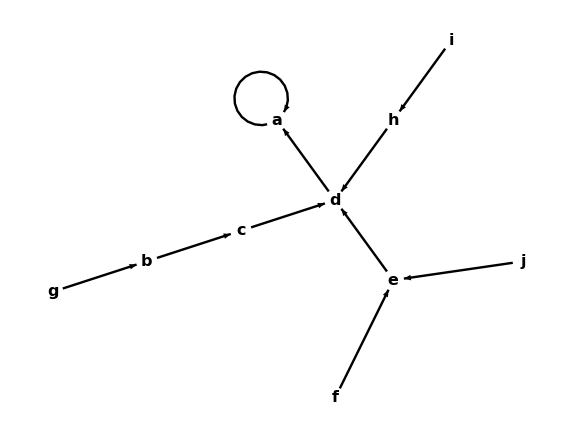

```mathematica
RuleGraph[ru1]
```

```mathematica
g[n_]:=Mod[n^2+1,13]
```

```mathematica
MakeFunctionRule[g,13]
{0->1,1->2,2->5,3->10,4->4,5->0,6->11,7->11,8->0,9->4,10->10,11->5,12->2}
```

{0→1,1→2,2→5,3→10,4→4,5→0,6→11,7→11,8→0,9→4,10→10,11→5,12→2}

{0→1,1→2,2→5,3→10,4→4,5→0,6→11,7→11,8→0,9→4,10→10,11→5,12→2}

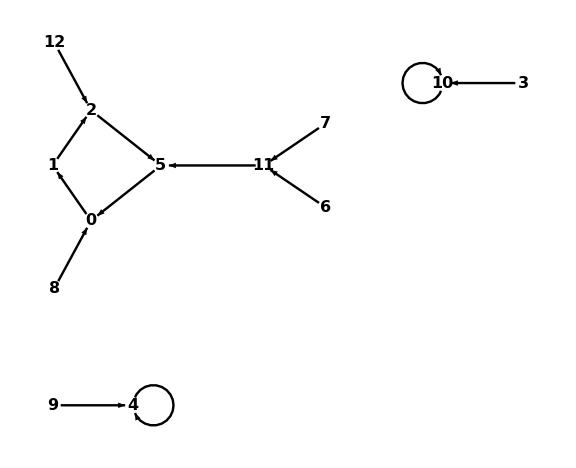

```mathematica
RuleGraph[MakeFunctionRule[g,13]]
```

```mathematica
h[n_]:=Mod[n^9,11]
```

```mathematica
MakeFunctionRule[h,11]
{0->0,1->1,2->6,3->4,4->3,5->9,6->2,7->8,8->7,9->5,10->10}
```

{0→0,1→1,2→6,3→4,4→3,5→9,6→2,7→8,8→7,9→5,10→10}

{0→0,1→1,2→6,3→4,4→3,5→9,6→2,7→8,8→7,9→5,10→10}

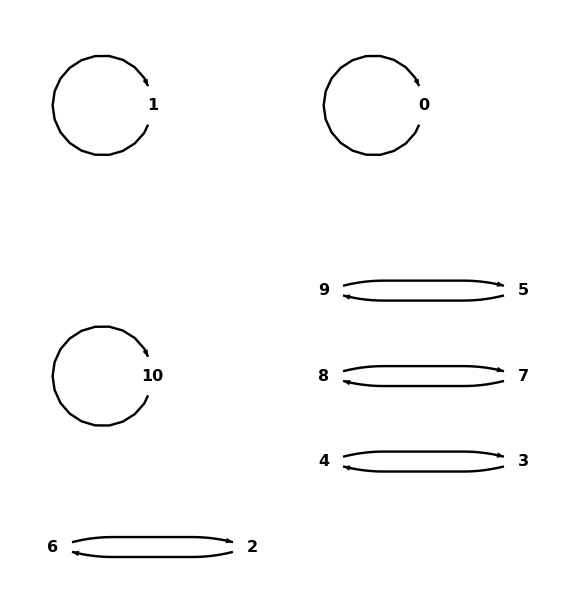

```mathematica
RuleGraph[MakeFunctionRule[h,11]]
```

```mathematica
k[n_]:=Mod[n^9+n^7+5n,11]
```

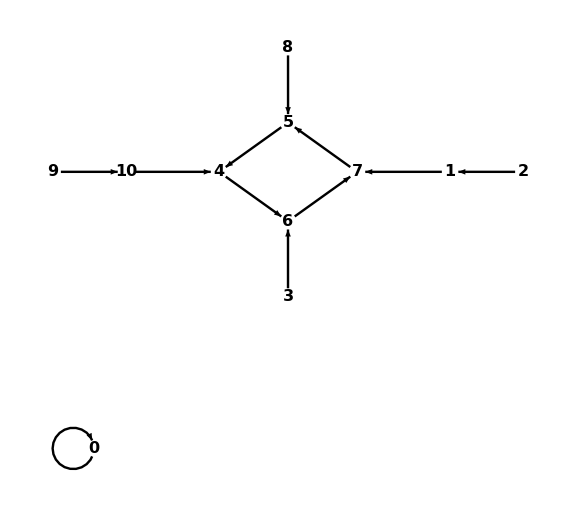

```mathematica
FunctionGraph[k,11]
```

```mathematica
s[n_]:=Mod[(n+1)^9+n^7+5n,11]
```

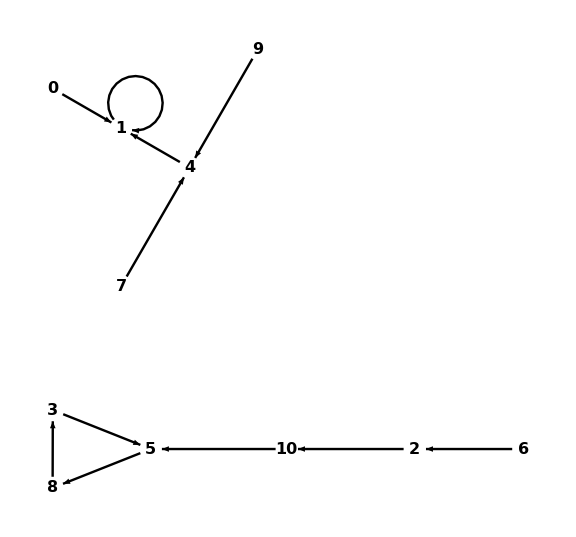

```mathematica
FunctionGraph[s,11]
```

```mathematica
aaa[n_]:=Mod[(n+1)^9+(n^+2)^7+5n,11]
```

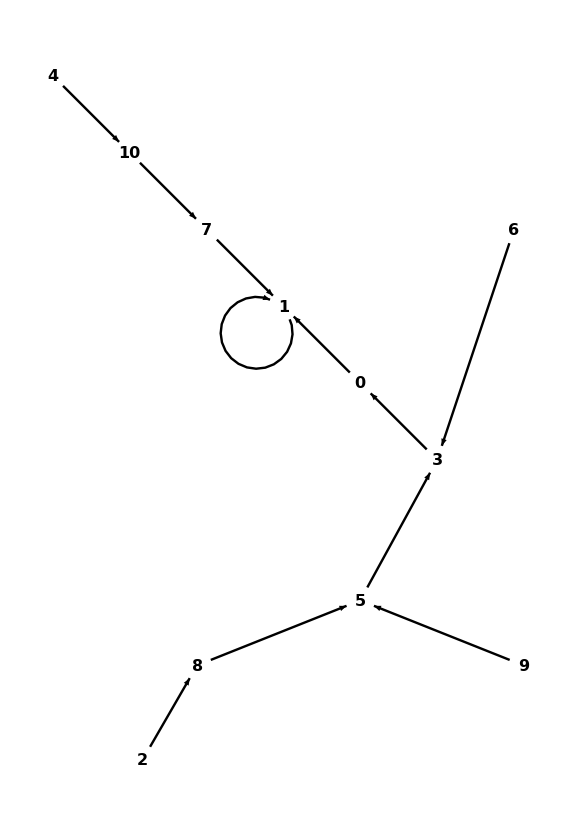

```mathematica
FunctionGraph[aaa,11]
```

```mathematica
bbb[n_]:=Mod[n^2+5,11]
```

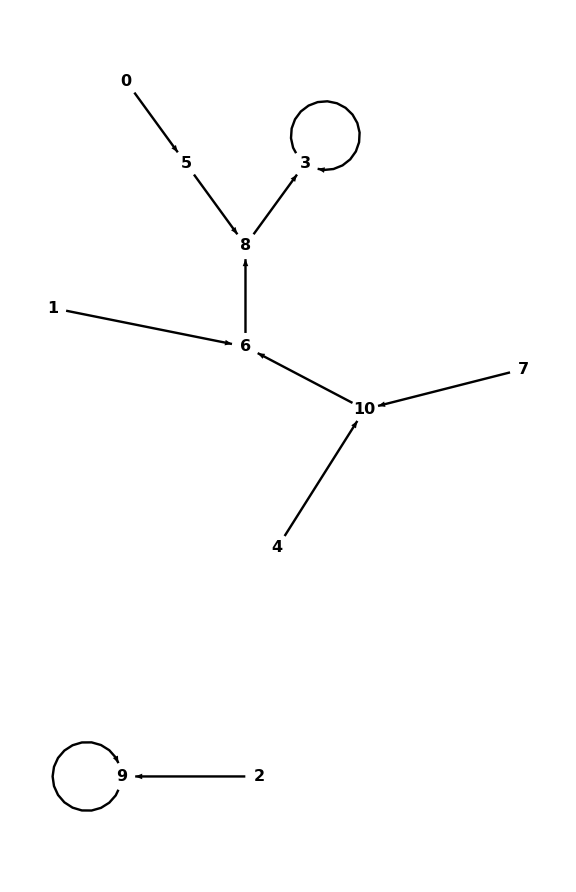

```mathematica
FunctionGraph[bbb,11]
```

```mathematica
ccc[n_]:=Mod[n^3+5,11]
```

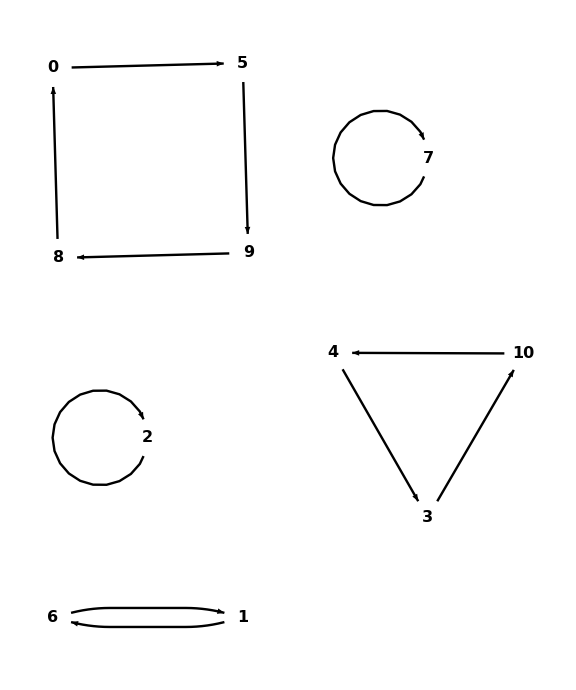

```mathematica
FunctionGraph[ccc,11]
```

```mathematica
ddd[n_]:=Mod[n^3+n^2,11]
```

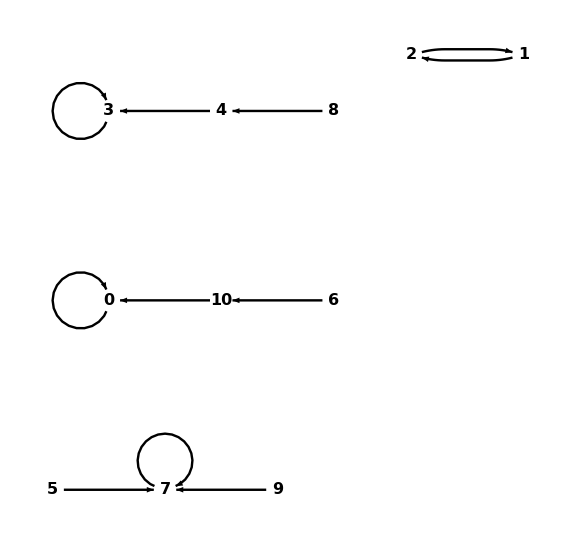

```mathematica
FunctionGraph[ddd,11]
```

```mathematica
Remove[g]
```

```mathematica
g[n_]:=Mod[n^2+1,11]
```

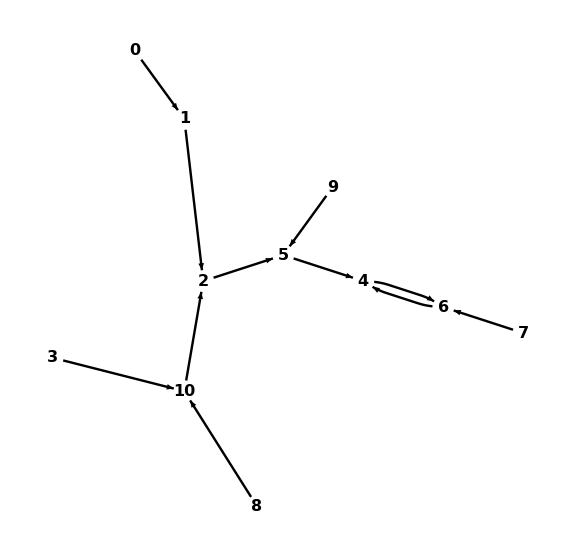

```mathematica
FunctionGraph[g,11]
```

```mathematica
gg[x_]:=g[g[x]]
```

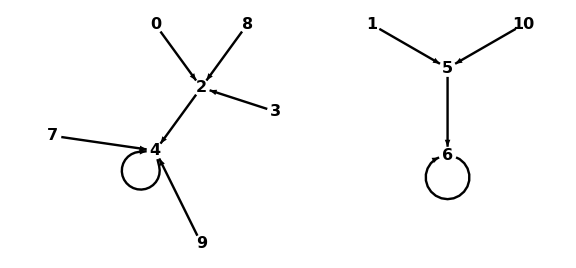

```mathematica
FunctionGraph[gg,11]
```

```mathematica
ggg[x_]:=g[g[g[x]]]
```

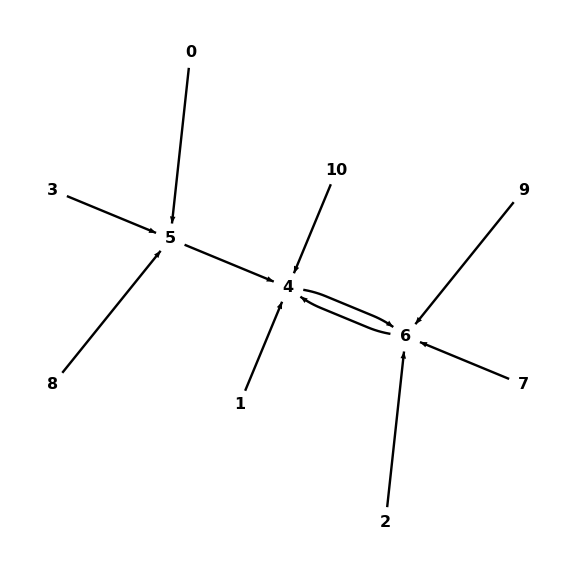

```mathematica
FunctionGraph[ggg,11]
```

```mathematica
ht[n_]:=Mod[n^(11),13]
```

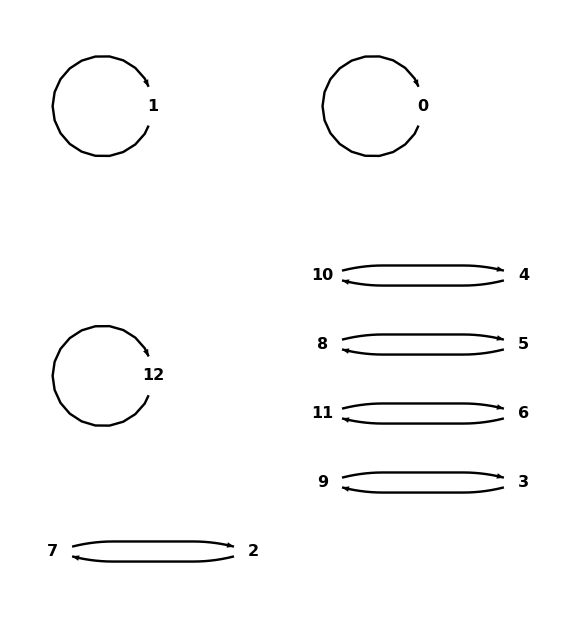

```mathematica
FunctionGraph[ht,13]
```

```mathematica
htx[n_]:=Mod[n^(11)+n^9+n^7+1,13]
```

```mathematica
htx[11]
```

4

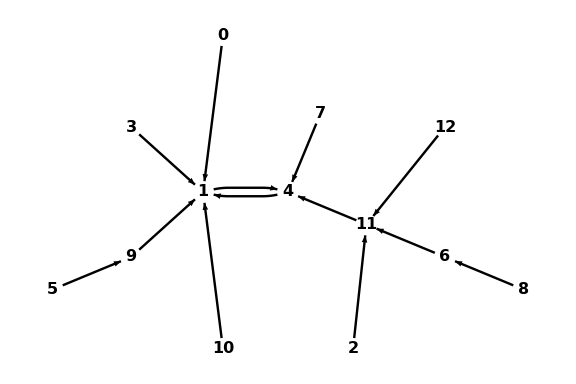

```mathematica
FunctionGraph[htx,13]
```

```mathematica
Table[{n,htx[n]},{n,0,12}]//tf
{{0, 1}, {1, 4}, {2, 11}, {3, 1}, {4, 1}, {5, 9}, {6, 11}, {7, 4}, {8, 6}, {9, 1}, {10, 1}, {11, 4}, {12, 11}}
```

0 | 1
1 | 4
2 | 11
3 | 1
4 | 1
5 | 9
6 | 11
7 | 4
8 | 6
9 | 1
10 | 1
11 | 4
12 | 11

{{0,1},{1,4},{2,11},{3,1},{4,1},{5,9},{6,11},{7,4},{8,6},{9,1},{10,1},{11,4},{12,11}}

```mathematica
fbig[0]:=5;fbig[1]:=2;fbig[2]:=13;fbig[3]:=4;fbig[4]=14;fbig[5]:=6;fbig[6]:=7;fbig[7]:=8;fbig[8]:=9;fbig[9]:=10;fbig[10]:=5;fbig[11]:=2;fbig[12]:=2;fbig[13]:=14;fbig[14]:=7;
```

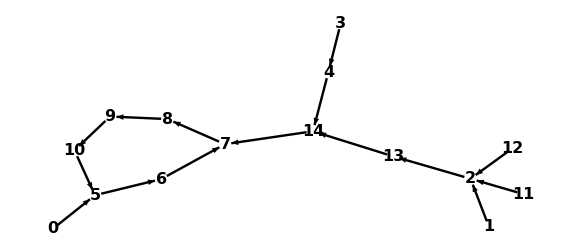

```mathematica
FunctionGraph[fbig,15]
```

### Composites of functions

```mathematica
ff["a"]:="a";ff["c"]:="d";ff["b"]:="c";ff["d"]:="a";ff["e"]:="d";ff["f"]:="e";ff["g"]:="b";ff["h"]:="d";ff["i"]:="h";ff["j"]:="e";
ff["c"]
"d"
ru2:=#->ff[#]&/@{"a","b","c","d","e","f","g","h","i","j"}
RuleGraph[ru2]
```

d

d

-Graphics-

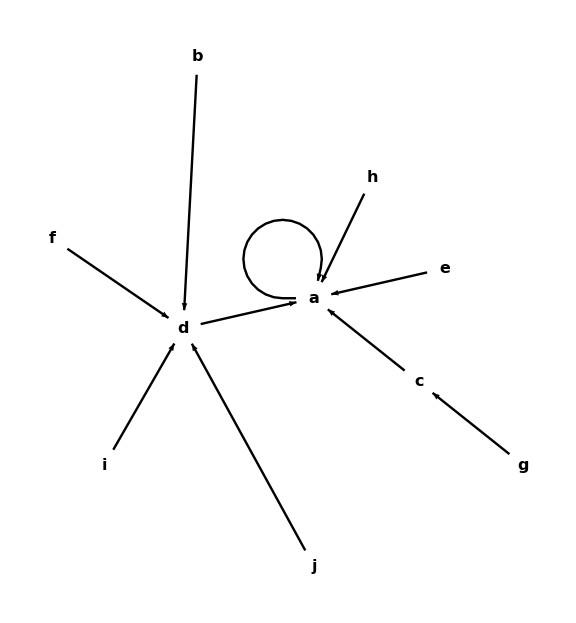

```mathematica
ru3:=#->ff[ff[#]]&/@{"a","b","c","d","e","f","g","h","i","j"}
RuleGraph[ru3]
```

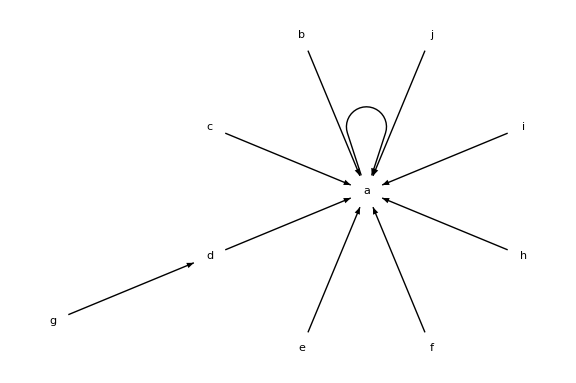

```mathematica
GraphPlot[#->ff[ff[ff[#]]]&/@{"a","b","c","d","e","f","g","h","i","j"},VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.02]],VertexRenderingFunction->(Text[#2,#1]&),ImageSize->Large]
```

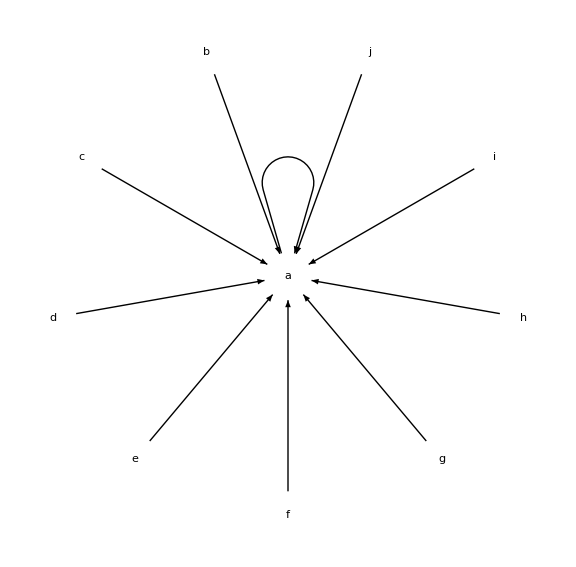

```mathematica
GraphPlot[#->ff[ff[ff[ff[#]]]]&/@{"a","b","c","d","e","f","g","h","i","j"},VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.02]],VertexRenderingFunction->(Text[#2,#1]&),ImageSize->Large]
```

### Sestina example

```mathematica
ee[0_,n_]:=n; ee[k_,n_]:=If[EvenQ[k],k/2,n-(k-1)/2]
```

```mathematica
ff[k_]:=ee[k,6]
```

```mathematica
Table[{k,k//ff,k//ff//ff},{k,1,6}]//TableForm
```

1 | 6 | 3
2 | 1 | 6
3 | 5 | 4
4 | 2 | 1
5 | 4 | 2
6 | 3 | 5

### Composition

### Permutations

### Inclusions

### Involutions

### Idempotents